```mathematica
Get[FindFile["JSONTools`"]]

imp3=Import["http://www.echo1001.me:5002/temperature","json"];
```

```mathematica
dim=Dimensions["temp"/.imp3]
```

{530}

```mathematica
Head@dim
```

List

```mathematica
init = "2017-10-03 22:22:00";
end = "2017-10-03 22:23:00";
init = StringReplace[init,Whitespace->"%20"];
end = StringReplace[end,Whitespace->"%20"];
imp = Import["http://www.echo1001.me:5002/temperature/"<>init<>"/"<>end,"json"];
imp
```

{data→{{DATETIME(created_at)→2017-10-03 22:22:01,temperature→30},{DATETIME(created_at)→2017-10-03 22:22:06,temperature→19},{DATETIME(created_at)→2017-10-03 22:22:11,temperature→31},{DATETIME(created_at)→2017-10-03 22:22:16,temperature→27},{DATETIME(created_at)→2017-10-03 22:22:21,temperature→23},{DATETIME(created_at)→2017-10-03 22:22:26,temperature→34},{DATETIME(created_at)→2017-10-03 22:22:31,temperature→16},{DATETIME(created_at)→2017-10-03 22:22:36,temperature→33},{DATETIME(created_at)→2017-10-03 22:22:41,temperature→31},{DATETIME(created_at)→2017-10-03 22:22:47,temperature→21},{DATETIME(created_at)→2017-10-03 22:22:52,temperature→21},{DATETIME(created_at)→2017-10-03 22:22:57,temperature→30}}}

```mathematica
Head@imp
```

List

```mathematica
date = imp[[1,2,;;,1,2]]
```

{2017-10-03 22:22:01,2017-10-03 22:22:06,2017-10-03 22:22:11,2017-10-03 22:22:16,2017-10-03 22:22:21,2017-10-03 22:22:26,2017-10-03 22:22:31,2017-10-03 22:22:36,2017-10-03 22:22:41,2017-10-03 22:22:47,2017-10-03 22:22:52,2017-10-03 22:22:57}

```mathematica
temp= imp[[1,2,;;,2,2]]
```

```mathematica
t={30,19,31,27,23,34,16,33,31,21,21,30};
```

```mathematica
ListPlot[temp]
```

-Graphics-

```mathematica
dim = Dimensions[temp];
t3 = Column[Table[temp[[i]],{i, dim[[1]]}]]
```

30
19
31
27
23
34
16
33
31
21
21
30

```mathematica
tempe = Table[temp[[i]],{i, dim[[1]]}]
```

{30,19,31,27,23,34,16,33,31,21,21,30}

```mathematica
Head@tempe
```

List

```mathematica
DateListPlot[date]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {2017-10-03 22:22:01,2017-10-03 22:22:06,2017-10-03 22:22:11,2017-10-03 22:22:16,2017-10-03 22:22:21,2017-10-03 22:22:26,2017-10-03 22:22:31,2017-10-03 22:22:36,2017-10-03 22:22:41,2017-10-03 22:22:47,2017-10-03 22:22:52,2017-10-03 22:22:57} is not a valid dataset or list of datasets.

DateListPlot[{2017-10-03 22:22:01,2017-10-03 22:22:06,2017-10-03 22:22:11,2017-10-03 22:22:16,2017-10-03 22:22:21,2017-10-03 22:22:26,2017-10-03 22:22:31,2017-10-03 22:22:36,2017-10-03 22:22:41,2017-10-03 22:22:47,2017-10-03 22:22:52,2017-10-03 22:22:57}]

```mathematica
temp
```

{30,19,31,27,23,34,16,33,31,21,21,30}

```mathematica
t1 = ToExpression["temp"]
```

{30,19,31,27,23,34,16,33,31,21,21,30}

```mathematica
Head@t1
```

List

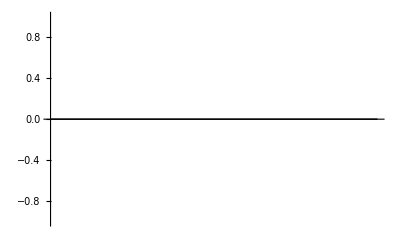

```mathematica
BarChart[temp]
```

```mathematica
t= imp[[1,2,;;,;;,2]]
```

{{2017-10-03 22:22:01,30},{2017-10-03 22:22:06,19},{2017-10-03 22:22:11,31},{2017-10-03 22:22:16,27},{2017-10-03 22:22:21,23},{2017-10-03 22:22:26,34},{2017-10-03 22:22:31,16},{2017-10-03 22:22:36,33},{2017-10-03 22:22:41,31},{2017-10-03 22:22:47,21},{2017-10-03 22:22:52,21},{2017-10-03 22:22:57,30}}

```mathematica
t = TableForm[t]
```

2017-10-03 22:22:01 | 30
2017-10-03 22:22:06 | 19
2017-10-03 22:22:11 | 31
2017-10-03 22:22:16 | 27
2017-10-03 22:22:21 | 23
2017-10-03 22:22:26 | 34
2017-10-03 22:22:31 | 16
2017-10-03 22:22:36 | 33
2017-10-03 22:22:41 | 31
2017-10-03 22:22:47 | 21
2017-10-03 22:22:52 | 21
2017-10-03 22:22:57 | 30

```mathematica
t
```

2017-10-03 22:22:01 | 30
2017-10-03 22:22:06 | 19
2017-10-03 22:22:11 | 31
2017-10-03 22:22:16 | 27
2017-10-03 22:22:21 | 23
2017-10-03 22:22:26 | 34
2017-10-03 22:22:31 | 16
2017-10-03 22:22:36 | 33
2017-10-03 22:22:41 | 31
2017-10-03 22:22:47 | 21
2017-10-03 22:22:52 | 21
2017-10-03 22:22:57 | 30

```mathematica
x =t[[1,1,All,2]]
y ={1,2,3,4,5,6,7,8,9,10,11,12}
```

{30,19,31,27,23,34,16,33,31,21,21,30}

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
data=Transpose[{x,y}]
```

{{30,1},{19,2},{31,3},{27,4},{23,5},{34,6},{16,7},{33,8},{31,9},{21,10},{21,11},{30,12}}

```mathematica
TableForm[data]
```

30 | 1
19 | 2
31 | 3
27 | 4
23 | 5
34 | 6
16 | 7
33 | 8
31 | 9
21 | 10
21 | 11
30 | 12

```mathematica
ListLinePlot[data]
```

-Graphics-